```mathematica
i10={{10.500,10.000,{1.00,41.85,1.55}},{10.650,10.000,{0.97,43.13,0.72}},{10.800,10.000,{0.93,44.79,0.69}},{10.950,10.000,{0.00,46.43,0.58}},{11.100,10.000,{0.00,49.08,0.64}},{11.250,10.000,{1.00,53.05,2.03}},{11.400,10.000,{1.00,54.09,2.14}},{11.550,10.000,{1.00,55.80,2.29}},{11.700,10.000,{0.00,58.90,0.80}},{11.850,10.000,{1.00,59.91,2.45}},{12.000,10.000,{0.91,62.02,1.02}}};
```

```mathematica
SolveNi[ii_]:=Module[{nc,data,weights,lf,a,b,c,ni,grad,err,foo},
nc=Min[ii[[All,2]]];
Assert[nc==Max[ii[[All,2]]]];
data={#[[1]],#[[3,1]]}&/@ii;
weights=1/(#[[3,2]])^2&/@ii;
lf=LinearModelFit[data,x,x,Weights->weights];
{a,b}=lf["BestFitParameters"];
c=lf["CovarianceMatrix"];
ni=(50-a)/b;
grad={-1/b,(a-50)/b^2};
err=Sqrt[grad.c.grad];
Print[Show[
ListPlot[{#[[1]],Around[#[[3,1]],#[[3,2]]]}&/@ii,AxesLabel->{"Ni","Ions"},
PlotLabel->StringTemplate["Nc = `1`, Ni = `2` ± `3`"][nc,ni,err]],
Plot[lf[x],{x,Min[ii[[All,1]]-1],Max[ii[[All,1]]+1]},PlotStyle->Orange],
Epilog->{PlotStyle->Black,Arrow[{{ni,60},{ni,51}}],Line[{{ni-err,50},{ni+err,50}}]}
]];
{nc,Around[ni,err]}
]
```

```mathematica
SolveNiScf[ii_]:=Module[{nc,data,weights,lf,a,b,c,ni,grad,err,foo},
nc=Min[ii[[All,2]]];
Assert[nc==Max[ii[[All,2]]]];
data={#[[1]],#[[3,2]]}&/@ii;
weights=1/(#[[3,3]])^2&/@ii;
lf=LinearModelFit[data,x,x,Weights->weights];
{a,b}=lf["BestFitParameters"];
c=lf["CovarianceMatrix"];
ni=(50-a)/b;
grad={-1/b,(a-50)/b^2};
err=Sqrt[grad.c.grad];
Print[Show[
ListPlot[{#[[1]],Around[#[[3,2]],#[[3,3]]]}&/@ii,AxesLabel->{"Ni","Ions"},
PlotLabel->StringTemplate["Nc = `1`, Ni = `2` ± `3`"][nc,ni,err]],
Plot[lf[x],{x,Min[ii[[All,1]]-1],Max[ii[[All,1]]+1]},PlotStyle->Orange],
Epilog->{PlotStyle->Black,Arrow[{{ni,60},{ni,51}}],Line[{{ni-err,50},{ni+err,50}}]}
]];
{nc,Around[ni,err]}
]
```

```mathematica
SolveNc[ii_]:=Module[{nc,data,weights,lf,a,b,c,ni,grad,err,foo},
ni=Min[ii[[All,1]]];
Assert[ni==Max[ii[[All,1]]]];
data={#[[2]],#[[3,1]]}&/@ii;
weights=1/(#[[3,2]])^2&/@ii;
lf=LinearModelFit[data,x,x,Weights->weights];
{a,b}=lf["BestFitParameters"];
c=lf["CovarianceMatrix"];
nc=(50-a)/b;
grad={-1/b,(a-50)/b^2};
err=Sqrt[grad.c.grad];
Print[Show[
ListPlot[{#[[2]],Around[#[[3,1]],#[[3,2]]]}&/@ii,AxesLabel->{"Nc","Ions"},
PlotLabel->StringTemplate["Ni = `1`, Nc = `2` ± `3`"][ni,nc,err]],
Plot[lf[x],{x,Min[ii[[All,2]]-1],Max[ii[[All,2]]+1]},PlotStyle->Orange],
Epilog->{PlotStyle->Black,Arrow[{{nc,60},{nc,51}}],Line[{{nc-err,50},{nc+err,50}}]}
]];
{Around[nc,err],ni}
]
```

```mathematica
i10
```

{{10.5,10.,{1.,41.85,1.55}},{10.65,10.,{0.97,43.13,0.72}},{10.8,10.,{0.93,44.79,0.69}},{10.95,10.,{0.,46.43,0.58}},{11.1,10.,{0.,49.08,0.64}},{11.25,10.,{1.,53.05,2.03}},{11.4,10.,{1.,54.09,2.14}},{11.55,10.,{1.,55.8,2.29}},{11.7,10.,{0.,58.9,0.8}},{11.85,10.,{1.,59.91,2.45}},{12.,10.,{0.91,62.02,1.02}}}

```mathematica
scfPaschenCurve={};
```

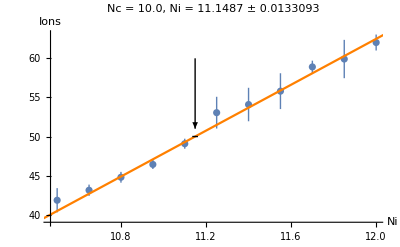

{10.,11.1490.013}

```mathematica
SolveNiScf[i10]
```

```mathematica
i17={{10.500,17.800,{1.00,38.54,0.97}},{10.605,17.800,{0.00,39.73,0.34}},{10.710,17.800,{0.00,41.56,0.36}},{10.815,17.800,{0.00,44.28,0.38}},{10.920,17.800,{0.00,45.49,0.40}},{11.025,17.800,{0.00,47.37,0.42}},{11.130,17.800,{0.00,50.12,0.44}},{11.235,17.800,{0.00,52.94,0.46}},{11.340,17.800,{1.00,53.90,1.47}},{11.445,17.800,{0.00,57.71,0.51}},{11.550,17.800,{1.00,61.57,1.64}}};
```

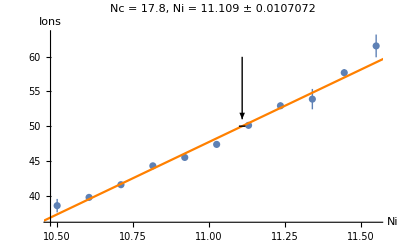

{17.8,11.1090.011}

```mathematica
SolveNiScf[i17]
```

```mathematica
i31={{12.400,31.600,{0.00,41.04,0.32}},{12.520,31.600,{0.00,44.46,0.34}},{12.640,31.600,{0.00,46.29,0.36}},{12.760,31.600,{0.00,48.78,0.37}},{12.880,31.600,{0.00,52.53,0.39}},{13.000,31.600,{0.00,54.46,0.42}},{13.120,31.600,{0.00,57.40,0.44}},{13.240,31.600,{0.00,61.30,0.47}},{13.360,31.600,{0.00,64.62,0.49}},{13.480,31.600,{0.00,68.48,0.53}},{13.600,31.600,{0.00,72.90,0.56}}};
```

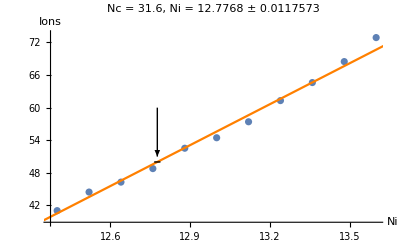

{31.6,12.7770.012}

```mathematica
SolveNiScf[i31]
```

```mathematica
AppendTo[scfPaschenCurve,%]
```

{{10.,11.1490.013},{17.8,11.1090.011},{31.6,12.7770.012}}

```mathematica
paschenCurve={{4.0320.006,100.},{6.4940.019,15.},{5.4690.017,20.},{10,11.2270.008},{17.8,11.0260.009},{31.6,12.6360.006},{56.2,15.5580.020},{100.,20.3500.025},{178.,27.800.05},{316.,39.460.04},{562.,57.980.07},{1000.,87.650.12}};
```

```mathematica
paschenCurveLV={#[[1]]/5,15#[[2]]}&/@paschenCurve
```

{{0.80630.0012,1500.},{1.2990.004,225.},{1.09370.0034,300.},{2,168.410.12},{3.56,165.390.14},{6.32,189.540.10},{11.24,233.370.29},{20.,305.20.4},{35.6,417.10.8},{63.2,591.80.6},{112.4,869.71.1},{200.,1314.81.8}}

```mathematica
scfPaschenCurveLV={#[[1]]/5.3,15#[[2]]}&/@scfPaschenCurve
```

{{1.88679,167.230.20},{3.35849,166.630.16},{5.96226,191.650.18}}

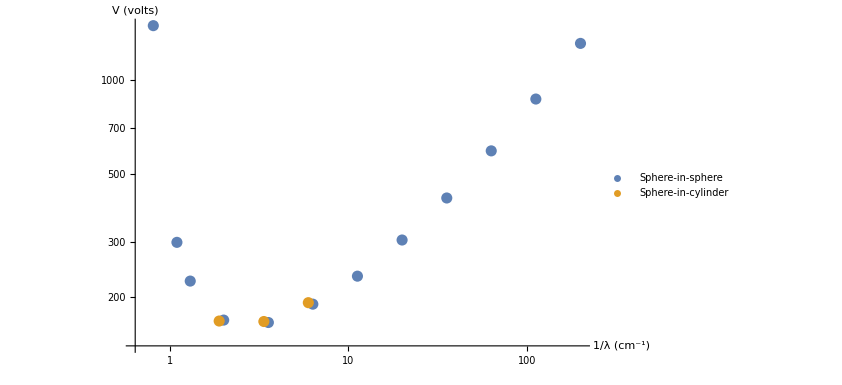

```mathematica
ListLogLogPlot[{paschenCurveLV,scfPaschenCurveLV},AxesLabel->{"1/λ (cm^-1)","V (volts)"},PlotLegends->{"Sphere-in-sphere","Sphere-in-cylinder"}]
```

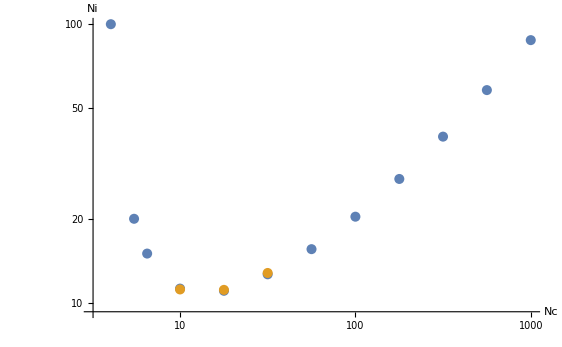

```mathematica
ListLogLogPlot[{paschenCurve,scfPaschenCurve},AxesLabel->{"Nc","Ni"}]
```

```mathematica
Sort[paschenCurve,#1[[1]]<#2[[1]]&]
```

{{6.4940.019,15.},{5.4690.017,20.},{10,11.2270.008},{17.8,11.0260.009},{31.6,12.6360.006},{56.2,15.5580.020},{100.,20.3500.025}}

```mathematica
cwCs1=Total[(cwNlf1["FitResiduals"]/(#[[3,2]]&/@cwVals1))^2]
```

12.5973

```mathematica
ExpFitter[vals_]:=Module[{nlf,chiSquare},
nlf=NonlinearModelFit[{#[[1]],#[[2,1]]}&/@vals,p1 Exp[p2 x]+p3,{p1,p2,p3},x,Weights->((1/(#[[2,2]])^2)&/@vals)];
Print[nlf];
Print[Show[ListPlot[{#[[1]],Around[#[[2,1]],#[[2,2]]]}&/@vals],Plot[nlf[x],{x,3,5}]]];
chiSquare=Total[(nlf["FitResiduals"]/(#[[2,2]]&/@vals))^2];
Print["Χ^2 = ",chiSquare];
nlf
];
```

FittedModel[-4.4034+1.7674 ⅇ^(0.852934 x)]

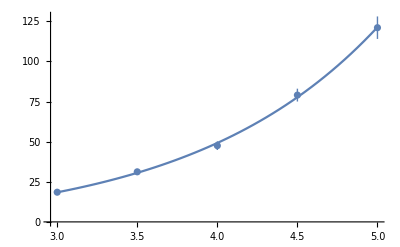

Χ^2 = 0.622512

```mathematica
ExpFitter[vals];
```

FittedModel[-3.28487+1.60157 ⅇ^(0.871451 x)]

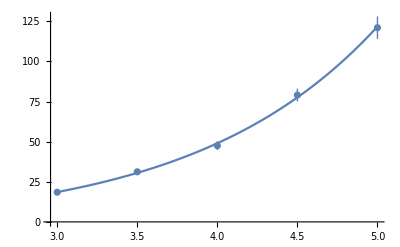

Χ^2 = 0.593408

```mathematica
ExpFitter[vals];
```

FittedModel[13.9946+0.179058 ⅇ^(1.28162 x)]

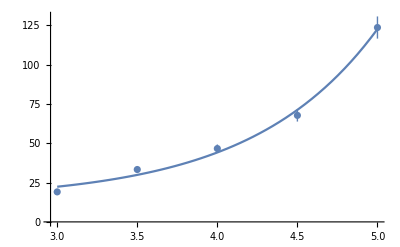

Χ^2 = 12.5973

```mathematica
ExpFitter[cwVals1[[All,2;;3]]];
```

FittedModel[2.18802+1.08588 ⅇ^(0.930871 x)]

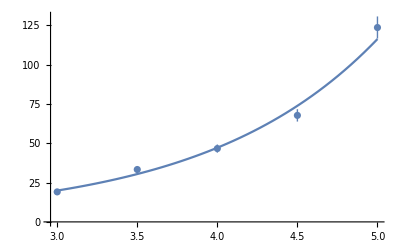

Χ^2 = 6.56454

```mathematica
ExpFitter[cwVals1[[All,2;;3]]];
```

```mathematica
cwVals1
```

{{100.,3.,{19.08,1.22}},{100.,3.5,{33.3,1.8}},{100.,4.,{46.62,2.58}},{100.,4.5,{67.71,3.92}},{100.,5.,{123.56,7.04}}}

```mathematica
cwVals1={{100.,3.,{19.08,1.22}},{100.,3.5,{33.3,1.8}},{100.,4.,{46.62,2.58}},{100.,4.5,{67.71,3.92}},{100.,5.,{123.56,7.04}}};
```

```mathematica
cwVals2={{100.000,3.000,{19.24,1.09}},{100.000,3.500,{29.72,1.75}},{100.000,4.000,{49.62,3.07}},{100.000,4.500,{82.67,4.52}},{100.000,5.000,{123.60,7.33}}};
```

FittedModel[-9.15922+2.47759 ⅇ^(0.797318 x)]

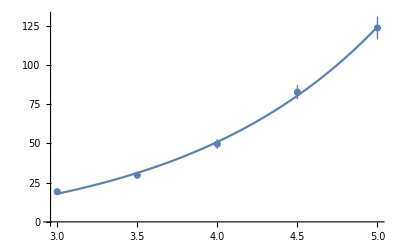

Χ^2 = 2.60626

```mathematica
ExpFitter[cwVals2[[All,2;;3]]];
```

FittedModel[-0.876236+1.21828 ⅇ^(0.930419 x)]

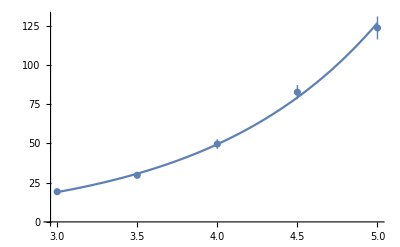

Χ^2 = 1.14659

```mathematica
ExpFitter[cwVals2[[All,2;;3]]];
```

```mathematica
cwVals3={{100.000,3.000,{17.71,1.00}},{100.000,3.500,{27.44,1.63}},{100.000,4.000,{47.25,3.16}},{100.000,4.500,{78.48,4.64}},{100.000,5.000,{129.88,7.11}}};
```

FittedModel[0.249599+0.793574 ⅇ^(1.01936 x)]

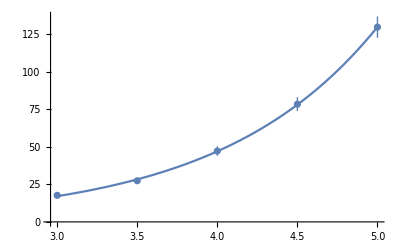

Χ^2 = 0.656764

```mathematica
ExpFitter[cwVals3[[All,2;;3]]];
```

FittedModel[2.73749+0.581989 ⅇ^(1.07906 x)]

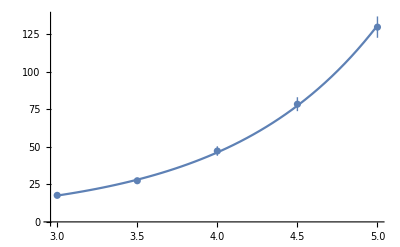

Χ^2 = 0.36799

```mathematica
ExpFitter[cwVals3[[All,2;;3]]];
```

```mathematica
cwVals4={{100.000,3.000,{17.36,0.97}},{100.000,3.500,{28.86,1.85}},{100.000,4.000,{46.99,2.40}},{100.000,4.500,{73.15,4.23}},{100.000,5.000,{123.75,7.09}}};
```

FittedModel[2.97084+0.673892 ⅇ^(1.03706 x)]

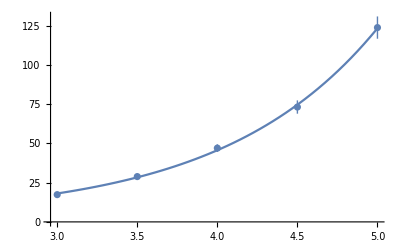

Χ^2 = 1.08932

```mathematica
ExpFitter[cwVals4[[All,2;;3]]];
```

FittedModel[-0.809542+1.04612 ⅇ^(0.952935 x)]

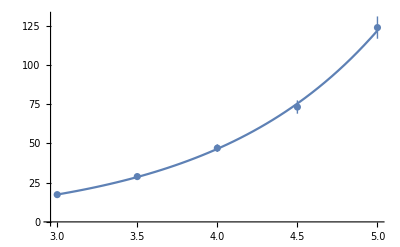

Χ^2 = 0.418961

```mathematica
ExpFitter[cwVals4[[All,2;;3]]];
```

```mathematica
cwVals5={{100.000,3.000,{18.20,0.35}},{100.000,3.500,{30.34,0.54}},{100.000,4.000,{48.22,0.88}},{100.000,4.500,{76.87,1.41}},{100.000,5.000,{121.15,2.24}}};
```

FittedModel[-2.84486+1.49279 ⅇ^(0.883906 x)]

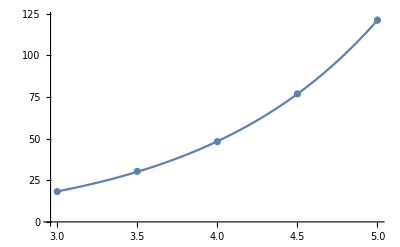

Χ^2 = 0.379302

```mathematica
ExpFitter[cwVals5[[All,2;;3]]];
```

FittedModel[-3.48668+1.58657 ⅇ^(0.872396 x)]

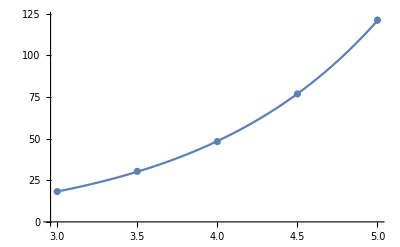

Χ^2 = 0.291491

```mathematica
ExpFitter[cwVals5[[All,2;;3]]];
```

```mathematica
cwVals6={{100.000,3.000,{18.31,0.34}},{100.000,3.500,{29.58,0.54}},{100.000,4.000,{48.75,0.87}},{100.000,4.500,{78.93,1.45}},{100.000,5.000,{122.09,2.22}}};
```

FittedModel[-5.82703+1.86682 ⅇ^(0.84582 x)]

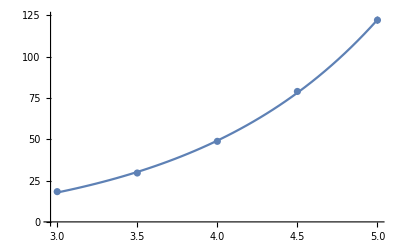

Χ^2 = 4.32461

```mathematica
ExpFitter[cwVals6[[All,2;;3]]];
```

FittedModel[-2.60814+1.39897 ⅇ^(0.899907 x)]

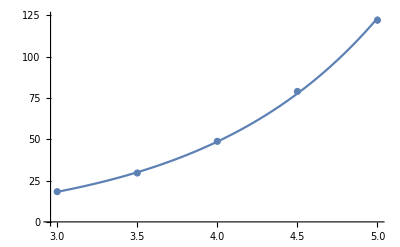

Χ^2 = 1.88155

```mathematica
ExpFitter[cwVals6[[All,2;;3]]];
```